```mathematica
(*x1c=0.21594827586206894;
x1f=0.19525862068965516;
x1z=0.2398706896551724;
y1c=0.41806451612903217;
y1f=0.34838709677419333;
y1z=0.487741935483871;
xbar=(x1c-x1f+x1z-x1c)/2;
ybar=(y1c-y1f+y1z-y1c)/2;
{Around[x1c,xbar],Around[y1c,ybar]}*)
```

```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
dcuE866data={{0.026400000000000035,1.087686567164179},
{0.038400000000000045,1.1436567164179103},
{0.052000000000000046,1.2220149253731343},
{0.06720000000000001,1.25},
{0.08160000000000003,1.3563432835820894},
{0.09680000000000002,1.3843283582089554},
{0.11200000000000002,1.4179104477611941},
{0.1264,1.630597014925373},
{0.1416,1.625},
{0.1608,1.585820895522388},
{0.1864,1.7089552238805972},
{0.21040000000000003,1.5634328358208955},
{0.236,1.4179104477611941},
{0.2688,1.087686567164179},
{0.3144,0.34888059701492535}
};
```

```mathematica
dcuE906data={{0.1472,1.4235074626865671},
{0.1784,1.3451492537313434},
{0.21519999999999995,1.4906716417910448},
{0.2624,1.4850746268656716},
{0.3144,1.6473880597014925},
{0.3848,1.580223880597015}
};
```

```mathematica
dmuE906={{0.1470873786407767,0.19096774193548385},
{0.17912621359223302,0.09419354838709676},
{0.21601941747572817,0.07032258064516128},
{0.26294498381877024,0.03548387096774186},
{0.31472491909385114,0.02064516129032251},
{0.3849514563106797,0.006451612903225767}
};
```

```mathematica
dmuE866={{0.11181229773462781,0.3219354838709677},
{0.1270226537216828,0.3390322580645161},
{0.1419093851132686,0.26},
{0.16100323624595467,0.18129032258064515},
{0.18592233009708736,0.14258064516129032},
{0.21100323624595468,0.08129032258064517},
{0.23608414239482206,0.04548387096774198},
{0.2690938511326861,0.007096774193548427},
{0.3150485436893204,-0.03999999999999998}
};
```

```mathematica
Hexdubardata={{0.0016853932584269815,0.01092436974789912},
{0.003932584269662948,0.03445378151260503},
{0.008426966292134852,0.06890756302521006},
{0.012359550561797772,0.08907563025210086},
{0.015168539325842723,0.11260504201680666},
{0.017977528089887646,0.126890756302521},
{0.020786516853932596,0.14285714285714285},
{0.023033707865168562,0.16386554621848737},
{0.027528089887640467,0.180672268907563},
{0.03033707865168539,0.20420168067226885},
{0.03426966292134834,0.22436974789915964},
{0.03876404494382024,0.24621848739495794},
{0.043258426966292146,0.2680672268907563},
{0.047191011235955066,0.28823529411764703},
{0.04943820224719103,0.303781512605042},
{0.05674157303370789,0.3285714285714285},
{0.061797752808988776,0.346218487394958},
{0.07303370786516855,0.3705882352941176},
{0.07921348314606744,0.38655462184873945},
{0.09213483146067417,0.4033613445378151},
{0.10449438202247194,0.41512605042016804},
{0.11910112359550559,0.41764705882352937},
{0.13202247191011238,0.41470588235294115},
{0.14438202247191015,0.4058823529411764},
{0.15168539325842692,0.3974789915966386},
{0.15786516853932583,0.39033613445378146},
{0.1662921348314607,0.3810924369747899},
{0.1780898876404494,0.3638655462184874},
{0.18820224719101122,0.35168067226890753},
{0.19550561797752805,0.34033613445378147},
{0.19999999999999998,0.32689075630252096},
{0.20786516853932582,0.31596638655462184},
{0.21573033707865166,0.30336134453781505},
{0.22528089887640448,0.2848739495798319},
{0.23707865168539324,0.2663865546218487},
{0.2528089887640449,0.2394957983193277},
{0.2696629213483146,0.21428571428571425},
{0.2808988764044943,0.19999999999999996},
{0.29157303370786514,0.17815126050420166},
{0.3050561797752809,0.1605042016806722},
{0.3134831460674158,0.1504201680672268},
{0.32191011235955047,0.13613445378151257},
{0.3387640449438202,0.11512605042016799},
{0.35,0.10420168067226887},
{0.36460674157303363,0.08991596638655464},
{0.3792134831460674,0.07563025210084029},
{0.396067415730337,0.06386554621848739},
{0.41067415730337065,0.055462184873949494},
{0.4241573033707865,0.042857142857142816},
{0.44269662921348296,0.03529411764705881},
{0.46292134831460663,0.026050420168067245},
{0.48370786516853925,0.02184873949579824},
{0.5016853932584269,0.015966386554621792},
{0.5191011235955055,0.014285714285714235},
{0.5376404494382021,0.010084033613445342},
{0.5623595505617976,0.004201680672268893},
{0.5853932584269661,0.004201680672268893},
{0.5983146067415729,0.0008403361344537785}
};
```

```mathematica
GlobalDataxdu1={{0.020063694267515954,0.03606683487128818},
{0.022611464968152903,0.037065476295499056},
{0.025159235668789845,0.038285724367909384},
{0.029617834394904494,0.039839441043103906},
{0.032802547770700664,0.040727632020043404},
{0.035987261146496856,0.04128341302468373},
{0.039171974522293034,0.04172839070522434},
{0.04235668789808921,0.042394975033964395},
{0.046178343949044624,0.0426186989431339},
{0.048726114649681566,0.04284171709864672},
{0.055095541401273936,0.04317765583922932},
{0.06656050955414017,0.042851597649840326},
{0.06273885350318475,0.043181890361169435},
{0.07292993630573252,0.04274432309402403},
{0.08057324840764335,0.04164052437496692},
{0.08885350318471341,0.040758685180937594},
{0.095859872611465,0.04009774688145103},
{0.1028662420382166,0.03899359528556558},
{0.11114649681528666,0.03822255941563597},
{0.11815286624203825,0.037229211143850235},
{0.1257961783439491,0.03590380577659368},
{0.13789808917197455,0.03369444395433774},
{0.14745222929936308,0.03203768724526704},
{0.15828025477707008,0.029716816345254686},
{0.16974522292993632,0.027617904970270123},
{0.17929936305732486,0.025628738288900256},
{0.19076433121019107,0.023529826913915693},
{0.20031847133757963,0.02165146355664555},
{0.20796178343949046,0.02032605818938899},
{0.217515923566879,0.01866930148031829},
{0.22898089171974526,0.016348783457134287},
{0.2385350318471338,0.015024436720362754},
{0.2493630573248408,0.013257582440849014},
{0.26210191082802553,0.011491786791820315},
{0.274203821656051,0.01005804823826243},
{0.2914012738853503,0.008294722727032126},
{0.3054140127388535,0.006972846128058992},
{0.32324840764331214,0.005542283465956199},
{0.34171974522292997,0.004444483652980925},
{0.360828025477707,0.00323623339273426},
{0.37675159235668787,0.0026910386929442226},
{0.39394904458598723,0.001924943098611423},
{0.4079617834394904,0.0017110997406355188},
{0.4213375796178344,0.0013861001817315616}
};
```

```mathematica
GlobalDataxdu2={{0.02070063694267519,0.024211232069446163},
{0.02388535031847136,0.026096652963283166},
{0.026433121019108302,0.027427704359793217},
{0.028980891719745244,0.02931277237680188},
{0.03280254777070066,0.03064452952696861},
{0.03662420382165608,0.03164387670483618},
{0.04171974522292996,0.032865536284559876},
{0.04617834394904461,0.034197646311554954},
{0.05191082802547773,0.0349764454717081},
{0.06019108280254779,0.03575665613917462},
{0.06910828025477711,0.03587239973887115},
{0.08121019108280256,0.03543589110221077},
{0.09012738853503188,0.034665208109109516},
{0.095859872611465,0.03378195740776682},
{0.10414012738853506,0.03301092153783722},
{0.11242038216560513,0.031796672371508725},
{0.11878980891719745,0.030359757926495756},
{0.12770700636942678,0.029145861636995608},
{0.13471337579617837,0.027709300068810984},
{0.14235668789808917,0.026162288053354976},
{0.15127388535031847,0.02439437514335621},
{0.16019108280254776,0.02295887220565661},
{0.17038216560509553,0.02108086172521481},
{0.1767515923566879,0.01964394728020184},
{0.18694267515923566,0.018098346772059213},
{0.19522292993630572,0.01666249095753127},
{0.2035031847133758,0.015448241791202778},
{0.21114649681528663,0.014233639748045944},
{0.21815286624203822,0.013129488152160487},
{0.2245222929936306,0.012135787003546408},
{0.23089171974522296,0.011474495827231507},
{0.2385350318471338,0.010259893784074665},
{0.24617834394904456,0.009266898389117276},
{0.25445859872611465,0.008385059195087953},
{0.260828025477707,0.007612964694673319},
{0.26910828025477707,0.006731125500643996},
{0.2773885350318471,0.005960089630714392},
{0.28885350318471337,0.004969211496727063},
{0.29904458598726114,0.004088430933182764},
{0.30923566878980896,0.003207650369638472},
{0.31751592356687897,0.0027690244720080387},
{0.3277070063694268,0.0024422605289623617},
{0.34171974522292997,0.0016744005504878423},
{0.3512738853503185,0.00145808705471355},
{0.36401273885350316,0.0010219312948815118},
{0.37675159235668787,0.0008073821832489322},
{0.38885350318471334,0.00048167687068827875},
{0.40159235668789806,0.00015632443495597337},
{0.4098726114649682,0.0001609118337244364},
{0.4207006369426751,0.00005610741570653832}
};
```

```mathematica
Seaquestdmudatawithbar={{0.1470.015,0.1920.033},{0.1790.017,0.0930.019},{0.2160.022,0.0700.011},{0.2630.025,0.0350.007},{0.3150.031,0.0210.007},{0.390.05,0.0060.006}};
```

```mathematica
E866dmudatawithbar={{0.1120.008,0.320.04},{0.1270.007,0.3390.034},{0.1420.008,0.2600.035},{0.1610.013,0.1810.027},{0.1860.012,0.1430.024},{0.2110.012,0.0810.022},{0.2360.012,0.0460.024},{0.2690.025,0.0060.019},{0.3150.025,-0.040.04}};
```

```mathematica
ap1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
mpd=I*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
mpu=I*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
dp1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ep1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
fp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
gp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
rsp1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
rsp1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
tup1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
tup1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
ap0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
dp0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
ep0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
fp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
gp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
mp0=I*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
rsp0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
tup0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
a=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-H-pi-zero.wdx"];
Ha=Query[1,1]@a;
Han=Interpolation[Flatten[Ha,1]];
Haf[x_,t_]=Han[x,t];

Ea=Query[2,1]@a;
Ean=Interpolation[Flatten[Ea,1]];
Eaf[x_,t_]=Ean[x,t];
```

```mathematica
d=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-H-pi-zero.wdx"];
Hd=Query[1,1]@d;
Hdn=Interpolation[Flatten[Hd,1]];
Hdf[x_,t_]=Hdn[x,t];

Ed=Query[2,1]@d;
Edf[x_,t_]=Ed;
```

```mathematica
e=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-H-pi-zero.wdx"];
He=Query[1,1]@e;
Hen=Interpolation[Flatten[He,1]];
Hef[x_,t_]=Hen[x,t];

Ee=Query[2,1]@e;
Eef[x_,t_]=Ee;
```

```mathematica
f=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-H-pi-zero.wdx"];
Hf=Query[1,1]@f;
Hfn=Interpolation[Flatten[Hf,1]];
Hff[x_,t_]=Hfn[x,t];

Ef=Query[2,1]@f;
Efn=Interpolation[Flatten[Ef,1]];
Eff[x_,t_]=Efn[x,t];
```

```mathematica
g=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-H-pi-zero.wdx"];
Hg=Query[1,1]@g;
Hgn=Interpolation[Flatten[Hg,1]];
Hgf[x_,t_]=Hgn[x,t];

Eg=Query[2,1]@g;
Egn=Interpolation[Flatten[Eg,1]];
Egf[x_,t_]=Egn[x,t];
```

```mathematica
m=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-H-pi-zero.wdx"];
Hm=Query[1,1]@m;
Hmn=Interpolation[Flatten[Hm,1]];
Hmf[x_,t_]=Hmn[x,t];

Em=Query[2,1]@m;
Emn=Interpolation[Flatten[Em,1]];
Emf[x_,t_]=Emn[x,t];
```

```mathematica
rs=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-H-pi-zero.wdx"];
Hrs=Query[1,1]@rs;
Hrsn=Interpolation[Flatten[Hrs,1]];
Hrsf[x_,t_]=Hrsn[x,t];

Ers=Query[2,1]@rs;
Ersn=Interpolation[Flatten[Ers,1]];
Ersf[x_,t_]=Ersn[x,t];
```

```mathematica
tu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-H-pi-zero.wdx"];
Htu=Query[1,1]@tu;
Htun=Interpolation[Flatten[Htu,1]];
Htuf[x_,t_]=Htun[x,t];

Etu=Query[2,1]@tu;
Etun=Interpolation[Flatten[Etu,1]];
Etuf[x_,t_]=Etun[x,t];
```

```mathematica
aL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-H-pi-zero-L08.wdx"];
HaL08=Query[1,1]@aL08;
HanL08=Interpolation[Flatten[HaL08,1]];
HafL08[x_,t_]=HanL08[x,t];

EaL08=Query[2,1]@aL08;
EanL08=Interpolation[Flatten[EaL08,1]];
EafL08[x_,t_]=EanL08[x,t];
dL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-H-pi-zero-L08.wdx"];
HdL08=Query[1,1]@dL08;
HdnL08=Interpolation[Flatten[HdL08,1]];
HdfL08[x_,t_]=HdnL08[x,t];

EdL08=Query[2,1]@dL08;
EdfL08[x_,t_]=EdL08;
eL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-H-pi-zero-L08.wdx"];
HeL08=Query[1,1]@eL08;
HenL08=Interpolation[Flatten[HeL08,1]];
HefL08[x_,t_]=HenL08[x,t];

EeL08=Query[2,1]@eL08;
EefL08[x_,t_]=EeL08;
fL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-H-pi-zero-L08.wdx"];
HfL08=Query[1,1]@fL08;
HfnL08=Interpolation[Flatten[HfL08,1]];
HffL08[x_,t_]=HfnL08[x,t];

EfL08=Query[2,1]@fL08;
EfnL08=Interpolation[Flatten[EfL08,1]];
EffL08[x_,t_]=EfnL08[x,t];
gL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-H-pi-zero-L08.wdx"];
HgL08=Query[1,1]@gL08;
HgnL08=Interpolation[Flatten[HgL08,1]];
HgfL08[x_,t_]=HgnL08[x,t];

EgL08=Query[2,1]@gL08;
EgnL08=Interpolation[Flatten[EgL08,1]];
EgfL08[x_,t_]=EgnL08[x,t];
mL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-H-pi-zero-L08.wdx"];
HmL08=Query[1,1]@mL08;
HmnL08=Interpolation[Flatten[HmL08,1]];
HmfL08[x_,t_]=HmnL08[x,t];

EmL08=Query[2,1]@mL08;
EmnL08=Interpolation[Flatten[EmL08,1]];
EmfL08[x_,t_]=EmnL08[x,t];
rsL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-H-pi-zero-L08.wdx"];
HrsL08=Query[1,1]@rsL08;
HrsnL08=Interpolation[Flatten[HrsL08,1]];
HrsfL08[x_,t_]=HrsnL08[x,t];

ErsL08=Query[2,1]@rsL08;
ErsnL08=Interpolation[Flatten[ErsL08,1]];
ErsfL08[x_,t_]=ErsnL08[x,t];
tuL08=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-H-pi-zero-L08.wdx"];
HtuL08=Query[1,1]@tuL08;
HtunL08=Interpolation[Flatten[HtuL08,1]];
HtufL08[x_,t_]=HtunL08[x,t];

EtuL08=Query[2,1]@tuL08;
EtunL08=Interpolation[Flatten[EtuL08,1]];
EtufL08[x_,t_]=EtunL08[x,t];
```

```mathematica
aL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-H-pi-zero-L09.wdx"];
HaL09=Query[1,1]@aL09;
HanL09=Interpolation[Flatten[HaL09,1]];
HafL09[x_,t_]=HanL09[x,t];

EaL09=Query[2,1]@aL09;
EanL09=Interpolation[Flatten[EaL09,1]];
EafL09[x_,t_]=EanL09[x,t];
dL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-H-pi-zero-L09.wdx"];
HdL09=Query[1,1]@dL09;
HdnL09=Interpolation[Flatten[HdL09,1]];
HdfL09[x_,t_]=HdnL09[x,t];

EdL09=Query[2,1]@dL09;
EdfL09[x_,t_]=EdL09;
eL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-H-pi-zero-L09.wdx"];
HeL09=Query[1,1]@eL09;
HenL09=Interpolation[Flatten[HeL09,1]];
HefL09[x_,t_]=HenL09[x,t];

EeL09=Query[2,1]@eL09;
EefL09[x_,t_]=EeL09;
fL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-H-pi-zero-L09.wdx"];
HfL09=Query[1,1]@fL09;
HfnL09=Interpolation[Flatten[HfL09,1]];
HffL09[x_,t_]=HfnL09[x,t];

EfL09=Query[2,1]@fL09;
EfnL09=Interpolation[Flatten[EfL09,1]];
EffL09[x_,t_]=EfnL09[x,t];
gL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-H-pi-zero-L09.wdx"];
HgL09=Query[1,1]@gL09;
HgnL09=Interpolation[Flatten[HgL09,1]];
HgfL09[x_,t_]=HgnL09[x,t];

EgL09=Query[2,1]@gL09;
EgnL09=Interpolation[Flatten[EgL09,1]];
EgfL09[x_,t_]=EgnL09[x,t];
mL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-H-pi-zero-L09.wdx"];
HmL09=Query[1,1]@mL09;
HmnL09=Interpolation[Flatten[HmL09,1]];
HmfL09[x_,t_]=HmnL09[x,t];

EmL09=Query[2,1]@mL09;
EmnL09=Interpolation[Flatten[EmL09,1]];
EmfL09[x_,t_]=EmnL09[x,t];
rsL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-H-pi-zero-L09.wdx"];
HrsL09=Query[1,1]@rsL09;
HrsnL09=Interpolation[Flatten[HrsL09,1]];
HrsfL09[x_,t_]=HrsnL09[x,t];

ErsL09=Query[2,1]@rsL09;
ErsnL09=Interpolation[Flatten[ErsL09,1]];
ErsfL09[x_,t_]=ErsnL09[x,t];
tuL09=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-H-pi-zero-L09.wdx"];
HtuL09=Query[1,1]@tuL09;
HtunL09=Interpolation[Flatten[HtuL09,1]];
HtufL09[x_,t_]=HtunL09[x,t];

EtuL09=Query[2,1]@tuL09;
EtunL09=Interpolation[Flatten[EtuL09,1]];
EtufL09[x_,t_]=EtunL09[x,t];
aL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-H-pi-zero-L11.wdx"];
HaL11=Query[1,1]@aL11;
HanL11=Interpolation[Flatten[HaL11,1]];
HafL11[x_,t_]=HanL11[x,t];

EaL11=Query[2,1]@aL11;
EanL11=Interpolation[Flatten[EaL11,1]];
EafL11[x_,t_]=EanL11[x,t];
dL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-H-pi-zero-L11.wdx"];
HdL11=Query[1,1]@dL11;
HdnL11=Interpolation[Flatten[HdL11,1]];
HdfL11[x_,t_]=HdnL11[x,t];

EdL11=Query[2,1]@dL11;
EdfL11[x_,t_]=EdL11;
eL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-H-pi-zero-L11.wdx"];
HeL11=Query[1,1]@eL11;
HenL11=Interpolation[Flatten[HeL11,1]];
HefL11[x_,t_]=HenL11[x,t];

EeL11=Query[2,1]@eL11;
EefL11[x_,t_]=EeL11;
fL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-H-pi-zero-L11.wdx"];
HfL11=Query[1,1]@fL11;
HfnL11=Interpolation[Flatten[HfL11,1]];
HffL11[x_,t_]=HfnL11[x,t];

EfL11=Query[2,1]@fL11;
EfnL11=Interpolation[Flatten[EfL11,1]];
EffL11[x_,t_]=EfnL11[x,t];
gL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-H-pi-zero-L11.wdx"];
HgL11=Query[1,1]@gL11;
HgnL11=Interpolation[Flatten[HgL11,1]];
HgfL11[x_,t_]=HgnL11[x,t];

EgL11=Query[2,1]@gL11;
EgnL11=Interpolation[Flatten[EgL11,1]];
EgfL11[x_,t_]=EgnL11[x,t];
mL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-H-pi-zero-L11.wdx"];
HmL11=Query[1,1]@mL11;
HmnL11=Interpolation[Flatten[HmL11,1]];
HmfL11[x_,t_]=HmnL11[x,t];

EmL11=Query[2,1]@mL11;
EmnL11=Interpolation[Flatten[EmL11,1]];
EmfL11[x_,t_]=EmnL11[x,t];
rsL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-H-pi-zero-L11.wdx"];
HrsL11=Query[1,1]@rsL11;
HrsnL11=Interpolation[Flatten[HrsL11,1]];
HrsfL11[x_,t_]=HrsnL11[x,t];

ErsL11=Query[2,1]@rsL11;
ErsnL11=Interpolation[Flatten[ErsL11,1]];
ErsfL11[x_,t_]=ErsnL11[x,t];
tuL11=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-H-pi-zero-L11.wdx"];
HtuL11=Query[1,1]@tuL11;
HtunL11=Interpolation[Flatten[HtuL11,1]];
HtufL11[x_,t_]=HtunL11[x,t];

EtuL11=Query[2,1]@tuL11;
EtunL11=Interpolation[Flatten[EtuL11,1]];
aL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-H-pi-zero-L12.wdx"];
HaL12=Query[1,1]@aL12;
HanL12=Interpolation[Flatten[HaL12,1]];
HafL12[x_,t_]=HanL12[x,t];

EaL12=Query[2,1]@aL12;
EanL12=Interpolation[Flatten[EaL12,1]];
EafL12[x_,t_]=EanL12[x,t];
dL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-H-pi-zero-L12.wdx"];
HdL12=Query[1,1]@dL12;
HdnL12=Interpolation[Flatten[HdL12,1]];
HdfL12[x_,t_]=HdnL12[x,t];

EdL12=Query[2,1]@dL12;
EdfL12[x_,t_]=EdL12;
eL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-H-pi-zero-L12.wdx"];
HeL12=Query[1,1]@eL12;
HenL12=Interpolation[Flatten[HeL12,1]];
HefL12[x_,t_]=HenL12[x,t];

EeL12=Query[2,1]@eL12;
EefL12[x_,t_]=EeL12;
fL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-H-pi-zero-L12.wdx"];
HfL12=Query[1,1]@fL12;
HfnL12=Interpolation[Flatten[HfL12,1]];
HffL12[x_,t_]=HfnL12[x,t];

EfL12=Query[2,1]@fL12;
EfnL12=Interpolation[Flatten[EfL12,1]];
EffL12[x_,t_]=EfnL12[x,t];
gL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-H-pi-zero-L12.wdx"];
HgL12=Query[1,1]@gL12;
HgnL12=Interpolation[Flatten[HgL12,1]];
HgfL12[x_,t_]=HgnL12[x,t];

EgL12=Query[2,1]@gL12;
EgnL12=Interpolation[Flatten[EgL12,1]];
EgfL12[x_,t_]=EgnL12[x,t];
mL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-H-pi-zero-L12.wdx"];
HmL12=Query[1,1]@mL12;
HmnL12=Interpolation[Flatten[HmL12,1]];
HmfL12[x_,t_]=HmnL12[x,t];

EmL12=Query[2,1]@mL12;
EmnL12=Interpolation[Flatten[EmL12,1]];
EmfL12[x_,t_]=EmnL12[x,t];
rsL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-H-pi-zero-L12.wdx"];
HrsL12=Query[1,1]@rsL12;
HrsnL12=Interpolation[Flatten[HrsL12,1]];
HrsfL12[x_,t_]=HrsnL12[x,t];

ErsL12=Query[2,1]@rsL12;
ErsnL12=Interpolation[Flatten[ErsL12,1]];
ErsfL12[x_,t_]=ErsnL12[x,t];
tuL12=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-H-pi-zero-L12.wdx"];
HtuL12=Query[1,1]@tuL12;
HtunL12=Interpolation[Flatten[HtuL12,1]];
HtufL12[x_,t_]=HtunL12[x,t];

EtuL12=Query[2,1]@tuL12;
EtunL12=Interpolation[Flatten[EtuL12,1]];
EtufL12[x_,t_]=EtunL12[x,t];
EtufL11[x_,t_]=EtunL11[x,t];
```

```mathematica
Had[x_,t_]=ap1*Haf[x,t];
Ead[x_,t_]=ap1*Eaf[x,t];
Hdd[x_,t_]=dp1*Hdf[x,t];
Edd[x_,t_]=dp1*Edf[x,t];
Hed[x_,t_]=ep1*Hef[x,t];
Eed[x_,t_]=ep1*Eef[x,t];
Hfd[x_,t_]=fp1*Hff[x,t];
Efd[x_,t_]=fp1*Eff[x,t];
Hgd[x_,t_]=gp1*Hgf[x,t];
Egd[x_,t_]=gp1*Egf[x,t];

Hap0d[x_,t_]=ap0*Haf[x,t];
Eap0d[x_,t_]=ap0*Eaf[x,t];
Hdp0d[x_,t_]=dp0*Hdf[x,t];
Edp0d[x_,t_]=dp0*Edf[x,t];
Hep0d[x_,t_]=ep0*Hef[x,t];
Eep0d[x_,t_]=ep0*Eef[x,t];
Hfp0d[x_,t_]=fp0*Hff[x,t];
Efp0d[x_,t_]=fp0*Eff[x,t];
Hgp0d[x_,t_]=gp0*Hgf[x,t];
Egp0d[x_,t_]=gp0*Egf[x,t];

Hap0u[x_,t_]=ap0*Haf[x,t];
Eap0u[x_,t_]=ap0*Eaf[x,t];
Hdp0u[x_,t_]=dp0*Hdf[x,t];
Edp0u[x_,t_]=dp0*Edf[x,t];
Hep0u[x_,t_]=ep0*Hef[x,t];
Eep0u[x_,t_]=ep0*Eef[x,t];
Hfp0u[x_,t_]=fp0*Hff[x,t];
Efp0u[x_,t_]=fp0*Eff[x,t];
Hgp0u[x_,t_]=gp0*Hgf[x,t];
Egp0u[x_,t_]=gp0*Egf[x,t];

Hmd[x_,t_]=mpd*Hmf[x,t];
Emd[x_,t_]=mpd*Emf[x,t];
Hmu[x_,t_]=mpu*Hmf[x,t];
Emu[x_,t_]=mpu*Emf[x,t];

Hmp0d[x_,t_]=mp0*Hmf[x,t];
Emp0d[x_,t_]=mp0*Emf[x,t];
Hmp0u[x_,t_]=mp0*Hmf[x,t];
Emp0u[x_,t_]=mp0*Emf[x,t];

Hrsd[x_,t_]=rsp1d*Hrsf[x,t];
Ersd[x_,t_]=rsp1d*Ersf[x,t];
Hrsu[x_,t_]=rsp1u*Hrsf[x,t];
Ersu[x_,t_]=rsp1u*Ersf[x,t];

Hrsp0d[x_,t_]=rsp0*Hrsf[x,t];
Ersp0d[x_,t_]=rsp0*Ersf[x,t];
Hrsp0u[x_,t_]=rsp0*Hrsf[x,t];
Ersp0u[x_,t_]=rsp0*Ersf[x,t];


Htud[x_,t_]=tup1d*Htuf[x,t];
Etud[x_,t_]=tup1d*Etuf[x,t];
Htuu[x_,t_]=tup1u*Htuf[x,t];
Etuu[x_,t_]=tup1u*Etuf[x,t];

Htup0d[x_,t_]=tup0*Htuf[x,t];
Etup0d[x_,t_]=tup0*Etuf[x,t];
Htup0u[x_,t_]=tup0*Htuf[x,t];
Etup0u[x_,t_]=tup0*Etuf[x,t];
```

```mathematica
HadL08[x_,t_]=ap1*HafL08[x,t];
EadL08[x_,t_]=ap1*EafL08[x,t];
HddL08[x_,t_]=dp1*HdfL08[x,t];
EddL08[x_,t_]=dp1*EdfL08[x,t];
HedL08[x_,t_]=ep1*HefL08[x,t];
EedL08[x_,t_]=ep1*EefL08[x,t];
HfdL08[x_,t_]=fp1*HffL08[x,t];
EfdL08[x_,t_]=fp1*EffL08[x,t];
HgdL08[x_,t_]=gp1*HgfL08[x,t];
EgdL08[x_,t_]=gp1*EgfL08[x,t];

Hap0dL08[x_,t_]=ap0*HafL08[x,t];
Eap0dL08[x_,t_]=ap0*EafL08[x,t];
Hdp0dL08[x_,t_]=dp0*HdfL08[x,t];
Edp0dL08[x_,t_]=dp0*EdfL08[x,t];
Hep0dL08[x_,t_]=ep0*HefL08[x,t];
Eep0dL08[x_,t_]=ep0*EefL08[x,t];
Hfp0dL08[x_,t_]=fp0*HffL08[x,t];
Efp0dL08[x_,t_]=fp0*EffL08[x,t];
Hgp0dL08[x_,t_]=gp0*HgfL08[x,t];
Egp0dL08[x_,t_]=gp0*EgfL08[x,t];

Hap0uL08[x_,t_]=ap0*HafL08[x,t];
Eap0uL08[x_,t_]=ap0*EafL08[x,t];
Hdp0uL08[x_,t_]=dp0*HdfL08[x,t];
Edp0uL08[x_,t_]=dp0*EdfL08[x,t];
Hep0uL08[x_,t_]=ep0*HefL08[x,t];
Eep0uL08[x_,t_]=ep0*EefL08[x,t];
Hfp0uL08[x_,t_]=fp0*HffL08[x,t];
Efp0uL08[x_,t_]=fp0*EffL08[x,t];
Hgp0uL08[x_,t_]=gp0*HgfL08[x,t];
Egp0uL08[x_,t_]=gp0*EgfL08[x,t];

HmdL08[x_,t_]=mpd*HmfL08[x,t];
EmdL08[x_,t_]=mpd*EmfL08[x,t];
HmuL08[x_,t_]=mpu*HmfL08[x,t];
EmuL08[x_,t_]=mpu*EmfL08[x,t];

Hmp0dL08[x_,t_]=mp0*HmfL08[x,t];
Emp0dL08[x_,t_]=mp0*EmfL08[x,t];
Hmp0uL08[x_,t_]=mp0*HmfL08[x,t];
Emp0uL08[x_,t_]=mp0*EmfL08[x,t];

HrsdL08[x_,t_]=rsp1d*HrsfL08[x,t];
ErsdL08[x_,t_]=rsp1d*ErsfL08[x,t];
HrsuL08[x_,t_]=rsp1u*HrsfL08[x,t];
ErsuL08[x_,t_]=rsp1u*ErsfL08[x,t];

Hrsp0dL08[x_,t_]=rsp0*HrsfL08[x,t];
Ersp0dL08[x_,t_]=rsp0*ErsfL08[x,t];
Hrsp0uL08[x_,t_]=rsp0*HrsfL08[x,t];
Ersp0uL08[x_,t_]=rsp0*ErsfL08[x,t];


HtudL08[x_,t_]=tup1d*HtufL08[x,t];
EtudL08[x_,t_]=tup1d*EtufL08[x,t];
HtuuL08[x_,t_]=tup1u*HtufL08[x,t];
EtuuL08[x_,t_]=tup1u*EtufL08[x,t];

Htup0dL08[x_,t_]=tup0*HtufL08[x,t];
Etup0dL08[x_,t_]=tup0*EtufL08[x,t];
Htup0uL08[x_,t_]=tup0*HtufL08[x,t];
Etup0uL08[x_,t_]=tup0*EtufL08[x,t];
HadL09[x_,t_]=ap1*HafL09[x,t];
EadL09[x_,t_]=ap1*EafL09[x,t];
HddL09[x_,t_]=dp1*HdfL09[x,t];
EddL09[x_,t_]=dp1*EdfL09[x,t];
HedL09[x_,t_]=ep1*HefL09[x,t];
EedL09[x_,t_]=ep1*EefL09[x,t];
HfdL09[x_,t_]=fp1*HffL09[x,t];
EfdL09[x_,t_]=fp1*EffL09[x,t];
HgdL09[x_,t_]=gp1*HgfL09[x,t];
EgdL09[x_,t_]=gp1*EgfL09[x,t];

Hap0dL09[x_,t_]=ap0*HafL09[x,t];
Eap0dL09[x_,t_]=ap0*EafL09[x,t];
Hdp0dL09[x_,t_]=dp0*HdfL09[x,t];
Edp0dL09[x_,t_]=dp0*EdfL09[x,t];
Hep0dL09[x_,t_]=ep0*HefL09[x,t];
Eep0dL09[x_,t_]=ep0*EefL09[x,t];
Hfp0dL09[x_,t_]=fp0*HffL09[x,t];
Efp0dL09[x_,t_]=fp0*EffL09[x,t];
Hgp0dL09[x_,t_]=gp0*HgfL09[x,t];
Egp0dL09[x_,t_]=gp0*EgfL09[x,t];

Hap0uL09[x_,t_]=ap0*HafL09[x,t];
Eap0uL09[x_,t_]=ap0*EafL09[x,t];
Hdp0uL09[x_,t_]=dp0*HdfL09[x,t];
Edp0uL09[x_,t_]=dp0*EdfL09[x,t];
Hep0uL09[x_,t_]=ep0*HefL09[x,t];
Eep0uL09[x_,t_]=ep0*EefL09[x,t];
Hfp0uL09[x_,t_]=fp0*HffL09[x,t];
Efp0uL09[x_,t_]=fp0*EffL09[x,t];
Hgp0uL09[x_,t_]=gp0*HgfL09[x,t];
Egp0uL09[x_,t_]=gp0*EgfL09[x,t];

HmdL09[x_,t_]=mpd*HmfL09[x,t];
EmdL09[x_,t_]=mpd*EmfL09[x,t];
HmuL09[x_,t_]=mpu*HmfL09[x,t];
EmuL09[x_,t_]=mpu*EmfL09[x,t];

Hmp0dL09[x_,t_]=mp0*HmfL09[x,t];
Emp0dL09[x_,t_]=mp0*EmfL09[x,t];
Hmp0uL09[x_,t_]=mp0*HmfL09[x,t];
Emp0uL09[x_,t_]=mp0*EmfL09[x,t];

HrsdL09[x_,t_]=rsp1d*HrsfL09[x,t];
ErsdL09[x_,t_]=rsp1d*ErsfL09[x,t];
HrsuL09[x_,t_]=rsp1u*HrsfL09[x,t];
ErsuL09[x_,t_]=rsp1u*ErsfL09[x,t];

Hrsp0dL09[x_,t_]=rsp0*HrsfL09[x,t];
Ersp0dL09[x_,t_]=rsp0*ErsfL09[x,t];
Hrsp0uL09[x_,t_]=rsp0*HrsfL09[x,t];
Ersp0uL09[x_,t_]=rsp0*ErsfL09[x,t];


HtudL09[x_,t_]=tup1d*HtufL09[x,t];
EtudL09[x_,t_]=tup1d*EtufL09[x,t];
HtuuL09[x_,t_]=tup1u*HtufL09[x,t];
EtuuL09[x_,t_]=tup1u*EtufL09[x,t];

Htup0dL09[x_,t_]=tup0*HtufL09[x,t];
Etup0dL09[x_,t_]=tup0*EtufL09[x,t];
Htup0uL09[x_,t_]=tup0*HtufL09[x,t];
Etup0uL09[x_,t_]=tup0*EtufL09[x,t];
HadL11[x_,t_]=ap1*HafL11[x,t];
EadL11[x_,t_]=ap1*EafL11[x,t];
HddL11[x_,t_]=dp1*HdfL11[x,t];
EddL11[x_,t_]=dp1*EdfL11[x,t];
HedL11[x_,t_]=ep1*HefL11[x,t];
EedL11[x_,t_]=ep1*EefL11[x,t];
HfdL11[x_,t_]=fp1*HffL11[x,t];
EfdL11[x_,t_]=fp1*EffL11[x,t];
HgdL11[x_,t_]=gp1*HgfL11[x,t];
EgdL11[x_,t_]=gp1*EgfL11[x,t];

Hap0dL11[x_,t_]=ap0*HafL11[x,t];
Eap0dL11[x_,t_]=ap0*EafL11[x,t];
Hdp0dL11[x_,t_]=dp0*HdfL11[x,t];
Edp0dL11[x_,t_]=dp0*EdfL11[x,t];
Hep0dL11[x_,t_]=ep0*HefL11[x,t];
Eep0dL11[x_,t_]=ep0*EefL11[x,t];
Hfp0dL11[x_,t_]=fp0*HffL11[x,t];
Efp0dL11[x_,t_]=fp0*EffL11[x,t];
Hgp0dL11[x_,t_]=gp0*HgfL11[x,t];
Egp0dL11[x_,t_]=gp0*EgfL11[x,t];

Hap0uL11[x_,t_]=ap0*HafL11[x,t];
Eap0uL11[x_,t_]=ap0*EafL11[x,t];
Hdp0uL11[x_,t_]=dp0*HdfL11[x,t];
Edp0uL11[x_,t_]=dp0*EdfL11[x,t];
Hep0uL11[x_,t_]=ep0*HefL11[x,t];
Eep0uL11[x_,t_]=ep0*EefL11[x,t];
Hfp0uL11[x_,t_]=fp0*HffL11[x,t];
Efp0uL11[x_,t_]=fp0*EffL11[x,t];
Hgp0uL11[x_,t_]=gp0*HgfL11[x,t];
Egp0uL11[x_,t_]=gp0*EgfL11[x,t];

HmdL11[x_,t_]=mpd*HmfL11[x,t];
EmdL11[x_,t_]=mpd*EmfL11[x,t];
HmuL11[x_,t_]=mpu*HmfL11[x,t];
EmuL11[x_,t_]=mpu*EmfL11[x,t];

Hmp0dL11[x_,t_]=mp0*HmfL11[x,t];
Emp0dL11[x_,t_]=mp0*EmfL11[x,t];
Hmp0uL11[x_,t_]=mp0*HmfL11[x,t];
Emp0uL11[x_,t_]=mp0*EmfL11[x,t];

HrsdL11[x_,t_]=rsp1d*HrsfL11[x,t];
ErsdL11[x_,t_]=rsp1d*ErsfL11[x,t];
HrsuL11[x_,t_]=rsp1u*HrsfL11[x,t];
ErsuL11[x_,t_]=rsp1u*ErsfL11[x,t];

Hrsp0dL11[x_,t_]=rsp0*HrsfL11[x,t];
Ersp0dL11[x_,t_]=rsp0*ErsfL11[x,t];
Hrsp0uL11[x_,t_]=rsp0*HrsfL11[x,t];
Ersp0uL11[x_,t_]=rsp0*ErsfL11[x,t];


HtudL11[x_,t_]=tup1d*HtufL11[x,t];
EtudL11[x_,t_]=tup1d*EtufL11[x,t];
HtuuL11[x_,t_]=tup1u*HtufL11[x,t];
EtuuL11[x_,t_]=tup1u*EtufL11[x,t];

Htup0dL11[x_,t_]=tup0*HtufL11[x,t];
Etup0dL11[x_,t_]=tup0*EtufL11[x,t];
Htup0uL11[x_,t_]=tup0*HtufL11[x,t];
Etup0uL11[x_,t_]=tup0*EtufL11[x,t];
HadL12[x_,t_]=ap1*HafL12[x,t];
EadL12[x_,t_]=ap1*EafL12[x,t];
HddL12[x_,t_]=dp1*HdfL12[x,t];
EddL12[x_,t_]=dp1*EdfL12[x,t];
HedL12[x_,t_]=ep1*HefL12[x,t];
EedL12[x_,t_]=ep1*EefL12[x,t];
HfdL12[x_,t_]=fp1*HffL12[x,t];
EfdL12[x_,t_]=fp1*EffL12[x,t];
HgdL12[x_,t_]=gp1*HgfL12[x,t];
EgdL12[x_,t_]=gp1*EgfL12[x,t];

Hap0dL12[x_,t_]=ap0*HafL12[x,t];
Eap0dL12[x_,t_]=ap0*EafL12[x,t];
Hdp0dL12[x_,t_]=dp0*HdfL12[x,t];
Edp0dL12[x_,t_]=dp0*EdfL12[x,t];
Hep0dL12[x_,t_]=ep0*HefL12[x,t];
Eep0dL12[x_,t_]=ep0*EefL12[x,t];
Hfp0dL12[x_,t_]=fp0*HffL12[x,t];
Efp0dL12[x_,t_]=fp0*EffL12[x,t];
Hgp0dL12[x_,t_]=gp0*HgfL12[x,t];
Egp0dL12[x_,t_]=gp0*EgfL12[x,t];

Hap0uL12[x_,t_]=ap0*HafL12[x,t];
Eap0uL12[x_,t_]=ap0*EafL12[x,t];
Hdp0uL12[x_,t_]=dp0*HdfL12[x,t];
Edp0uL12[x_,t_]=dp0*EdfL12[x,t];
Hep0uL12[x_,t_]=ep0*HefL12[x,t];
Eep0uL12[x_,t_]=ep0*EefL12[x,t];
Hfp0uL12[x_,t_]=fp0*HffL12[x,t];
Efp0uL12[x_,t_]=fp0*EffL12[x,t];
Hgp0uL12[x_,t_]=gp0*HgfL12[x,t];
Egp0uL12[x_,t_]=gp0*EgfL12[x,t];

HmdL12[x_,t_]=mpd*HmfL12[x,t];
EmdL12[x_,t_]=mpd*EmfL12[x,t];
HmuL12[x_,t_]=mpu*HmfL12[x,t];
EmuL12[x_,t_]=mpu*EmfL12[x,t];

Hmp0dL12[x_,t_]=mp0*HmfL12[x,t];
Emp0dL12[x_,t_]=mp0*EmfL12[x,t];
Hmp0uL12[x_,t_]=mp0*HmfL12[x,t];
Emp0uL12[x_,t_]=mp0*EmfL12[x,t];

HrsdL12[x_,t_]=rsp1d*HrsfL12[x,t];
ErsdL12[x_,t_]=rsp1d*ErsfL12[x,t];
HrsuL12[x_,t_]=rsp1u*HrsfL12[x,t];
ErsuL12[x_,t_]=rsp1u*ErsfL12[x,t];

Hrsp0dL12[x_,t_]=rsp0*HrsfL12[x,t];
Ersp0dL12[x_,t_]=rsp0*ErsfL12[x,t];
Hrsp0uL12[x_,t_]=rsp0*HrsfL12[x,t];
Ersp0uL12[x_,t_]=rsp0*ErsfL12[x,t];


HtudL12[x_,t_]=tup1d*HtufL12[x,t];
EtudL12[x_,t_]=tup1d*EtufL12[x,t];
HtuuL12[x_,t_]=tup1u*HtufL12[x,t];
EtuuL12[x_,t_]=tup1u*EtufL12[x,t];

Htup0dL12[x_,t_]=tup0*HtufL12[x,t];
Etup0dL12[x_,t_]=tup0*EtufL12[x,t];
Htup0uL12[x_,t_]=tup0*HtufL12[x,t];
Etup0uL12[x_,t_]=tup0*EtufL12[x,t];
```

```mathematica
(*(dbar-ubar)*)
```

```mathematica
Hdubar[x_,t_]=Had[x,t]+Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hmd[x,t]+Hrsd[x,t]+Htud[x,t]-(Hmu[x,t]+Hrsu[x,t]+Htuu[x,t]);
Edubar[x_,t_]=Ead[x,t]+Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Emd[x,t]+Ersd[x,t]+Etud[x,t]-(Emu[x,t]+Ersu[x,t]+Etuu[x,t]);
```

```mathematica
HdubarL08[x_,t_]=HadL08[x,t]+HddL08[x,t]+HedL08[x,t]+HfdL08[x,t]+HgdL08[x,t]+HmdL08[x,t]+HrsdL08[x,t]+HtudL08[x,t]-(HmuL08[x,t]+HrsuL08[x,t]+HtuuL08[x,t]);
EdubarL08[x_,t_]=EadL08[x,t]+EddL08[x,t]+EedL08[x,t]+EfdL08[x,t]+EgdL08[x,t]+EmdL08[x,t]+ErsdL08[x,t]+EtudL08[x,t]-(EmuL08[x,t]+ErsuL08[x,t]+EtuuL08[x,t]);
HdubarL09[x_,t_]=HadL09[x,t]+HddL09[x,t]+HedL09[x,t]+HfdL09[x,t]+HgdL09[x,t]+HmdL09[x,t]+HrsdL09[x,t]+HtudL09[x,t]-(HmuL09[x,t]+HrsuL09[x,t]+HtuuL09[x,t]);
EdubarL09[x_,t_]=EadL09[x,t]+EddL09[x,t]+EedL09[x,t]+EfdL09[x,t]+EgdL09[x,t]+EmdL09[x,t]+ErsdL09[x,t]+EtudL09[x,t]-(EmuL09[x,t]+ErsuL09[x,t]+EtuuL09[x,t]);
HdubarL11[x_,t_]=HadL11[x,t]+HddL11[x,t]+HedL11[x,t]+HfdL11[x,t]+HgdL11[x,t]+HmdL11[x,t]+HrsdL11[x,t]+HtudL11[x,t]-(HmuL11[x,t]+HrsuL11[x,t]+HtuuL11[x,t]);
EdubarL11[x_,t_]=EadL11[x,t]+EddL11[x,t]+EedL11[x,t]+EfdL11[x,t]+EgdL11[x,t]+EmdL11[x,t]+ErsdL11[x,t]+EtudL11[x,t]-(EmuL11[x,t]+ErsuL11[x,t]+EtuuL11[x,t]);
HdubarL12[x_,t_]=HadL12[x,t]+HddL12[x,t]+HedL12[x,t]+HfdL12[x,t]+HgdL12[x,t]+HmdL12[x,t]+HrsdL12[x,t]+HtudL12[x,t]-(HmuL12[x,t]+HrsuL12[x,t]+HtuuL12[x,t]);
EdubarL12[x_,t_]=EadL12[x,t]+EddL12[x,t]+EedL12[x,t]+EfdL12[x,t]+EgdL12[x,t]+EmdL12[x,t]+ErsdL12[x,t]+EtudL12[x,t]-(EmuL12[x,t]+ErsuL12[x,t]+EtuuL12[x,t]);
```

```mathematica
(*dbar/ubar*)
```

```mathematica
Hdude[x_,t_]=(Had[x,t]+Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hmd[x,t]+Hrsd[x,t]+Htud[x,t]+Hap0d[x,t]+Hdp0d[x,t]+Hep0d[x,t]+Hfp0d[x,t]+Hgp0d[x,t]+Hmp0d[x,t]+Hrsp0d[x,t]+Htup0d[x,t])/(Hmu[x,t]+Hrsu[x,t]+Htuu[x,t]+Hap0u[x,t]+Hdp0u[x,t]+Hep0u[x,t]+Hfp0u[x,t]+Hgp0u[x,t]+Hmp0u[x,t]+Hrsp0u[x,t]+Htup0u[x,t]);
Edude[x_,t_]=(Ead[x,t]+Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Emd[x,t]+Ersd[x,t]+Etud[x,t]+Eap0d[x,t]+Edp0d[x,t]+Eep0d[x,t]+Efp0d[x,t]+Egp0d[x,t]+Emp0d[x,t]+Ersp0d[x,t]+Etup0d[x,t])/(Emu[x,t]+Ersu[x,t]+Etuu[x,t]+Eap0u[x,t]+Edp0u[x,t]+Eep0u[x,t]+Efp0u[x,t]+Egp0u[x,t]+Emp0u[x,t]+Ersp0u[x,t]+Etup0u[x,t]);
```

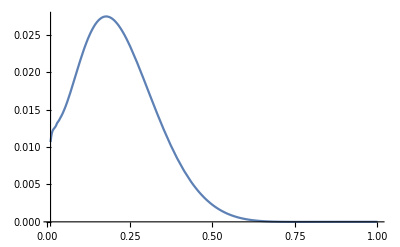

```mathematica
Plot[x*Hdubar[x,0],{x,0.01,1}]
```

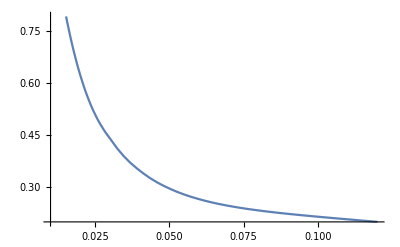

```mathematica
Plot[Hdubar[x,0],{x,0.01,0.12}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

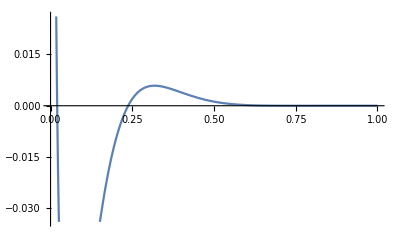

```mathematica
Plot[Hdubar[x,-1],{x,0,1}]
```

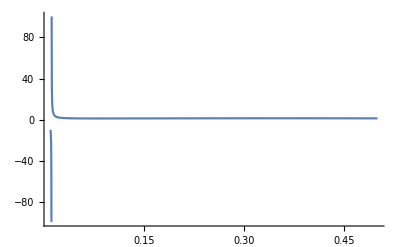

```mathematica
Plot[Hdude[x,0],{x,0.01,0.5},PlotRange->All]
```

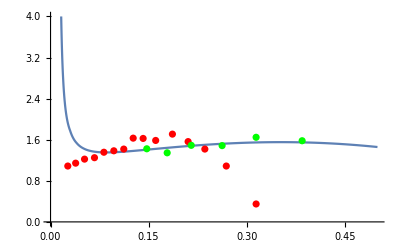

```mathematica
Show[Plot[Hdude[x,0],{x,0.01,0.5},PlotRange->{Automatic,{0,4}}],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```

```mathematica
Hdude[0.31,0]
```

1.54559+0. ⅈ

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

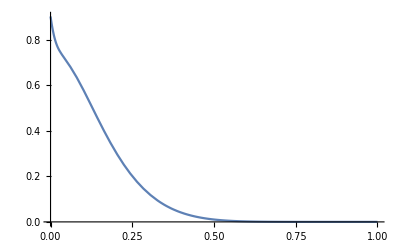

```mathematica
Plot[Had[x,0]+Hdd[x,0]+Hed[x,0]+Hfd[x,0]+Hgd[x,0]+Hmd[x,0]+Hrsd[x,0]+Htud[x,0],{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

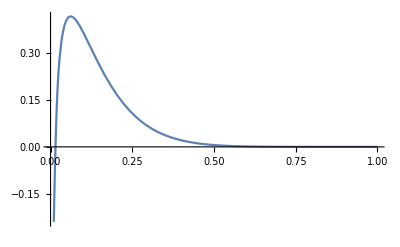

```mathematica
Plot[Hmu[x,0]+Hrsu[x,0]+Htuu[x,0],{x,0,1}]
```

```mathematica
Hmeson[x_,t_]=Had[x,t]+Hmd[x,t]-(Hmu[x,t]);
Emeson[x_,t_]=Ead[x,t]+Emd[x,t]-(Emu[x,t]);
```

```mathematica
HmesonL08[x_,t_]=HadL08[x,t]+HmdL08[x,t]-(HmuL08[x,t]);
EmesonL08[x_,t_]=EadL08[x,t]+EmdL08[x,t]-(EmuL08[x,t]);
HmesonL09[x_,t_]=HadL09[x,t]+HmdL09[x,t]-(HmuL09[x,t]);
EmesonL09[x_,t_]=EadL09[x,t]+EmdL09[x,t]-(EmuL09[x,t]);
HmesonL11[x_,t_]=HadL11[x,t]+HmdL11[x,t]-(HmuL11[x,t]);
EmesonL11[x_,t_]=EadL11[x,t]+EmdL11[x,t]-(EmuL11[x,t]);
HmesonL12[x_,t_]=HadL12[x,t]+HmdL12[x,t]-(HmuL12[x,t]);
EmesonL12[x_,t_]=EadL12[x,t]+EmdL12[x,t]-(EmuL12[x,t]);
```

```mathematica
Hmede[x_,t_]=(Had[x,t]+Hmd[x,t]+Hap0d[x,t]+Hmp0d[x,t])/(Hmu[x,t]+Hap0u[x,t]+Hmp0u[x,t]);
Emede[x_,t_]=(Ead[x,t]+Emd[x,t]+Eap0d[x,t]+Emp0d[x,t])/(Emu[x,t]+Eap0u[x,t]+Emp0u[x,t]);
```

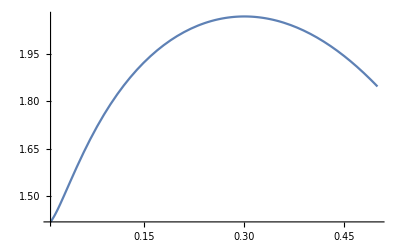

```mathematica
Plot[Hmede[x,0],{x,0.01,0.5}]
```

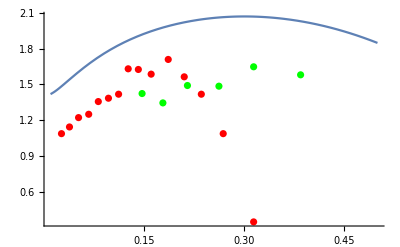

```mathematica
Show[Plot[Hmede[x,0],{x,0.01,0.5},PlotRange->All],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```

```mathematica
Hmede[0.31,0]
```

2.06832+0. ⅈ

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

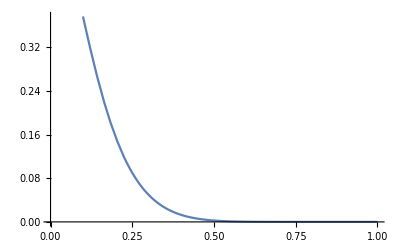

```mathematica
Plot[Hmeson[x,0],{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,-0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

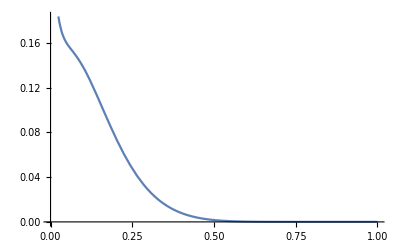

```mathematica
Plot[Hmeson[x,-0.25],{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

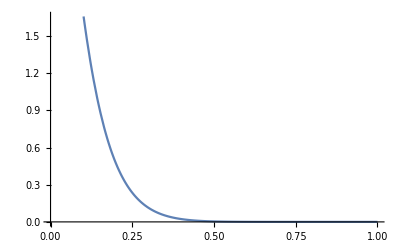

```mathematica
Plot[Emeson[x,0],{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,-0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

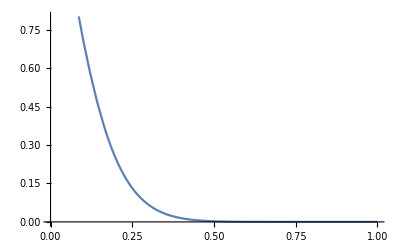

```mathematica
Plot[Emeson[x,-0.25],{x,0,1}]
```

```mathematica
Hkr[x_,t_]=Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hrsd[x,t]+Htud[x,t]-(Hrsu[x,t]+Htuu[x,t]);
Ekr[x_,t_]=Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Ersd[x,t]+Etud[x,t]-(Ersu[x,t]+Etuu[x,t]);
```

```mathematica
HkrL08[x_,t_]=HddL08[x,t]+HedL08[x,t]+HfdL08[x,t]+HgdL08[x,t]+HrsdL08[x,t]+HtudL08[x,t]-(HrsuL08[x,t]+HtuuL08[x,t]);
EkrL08[x_,t_]=EddL08[x,t]+EedL08[x,t]+EfdL08[x,t]+EgdL08[x,t]+ErsdL08[x,t]+EtudL08[x,t]-(ErsuL08[x,t]+EtuuL08[x,t]);
HkrL12[x_,t_]=HddL12[x,t]+HedL12[x,t]+HfdL12[x,t]+HgdL12[x,t]+HrsdL12[x,t]+HtudL12[x,t]-(HrsuL12[x,t]+HtuuL12[x,t]);
EkrL12[x_,t_]=EddL12[x,t]+EedL12[x,t]+EfdL12[x,t]+EgdL12[x,t]+ErsdL12[x,t]+EtudL12[x,t]-(ErsuL12[x,t]+EtuuL12[x,t]);
HkrL11[x_,t_]=HddL11[x,t]+HedL11[x,t]+HfdL11[x,t]+HgdL11[x,t]+HrsdL11[x,t]+HtudL11[x,t]-(HrsuL11[x,t]+HtuuL11[x,t]);
EkrL11[x_,t_]=EddL11[x,t]+EedL11[x,t]+EfdL11[x,t]+EgdL11[x,t]+ErsdL11[x,t]+EtudL11[x,t]-(ErsuL11[x,t]+EtuuL11[x,t]);
HkrL09[x_,t_]=HddL09[x,t]+HedL09[x,t]+HfdL09[x,t]+HgdL09[x,t]+HrsdL09[x,t]+HtudL09[x,t]-(HrsuL09[x,t]+HtuuL09[x,t]);
EkrL09[x_,t_]=EddL09[x,t]+EedL09[x,t]+EfdL09[x,t]+EgdL09[x,t]+ErsdL09[x,t]+EtudL09[x,t]-(ErsuL09[x,t]+EtuuL09[x,t]);
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

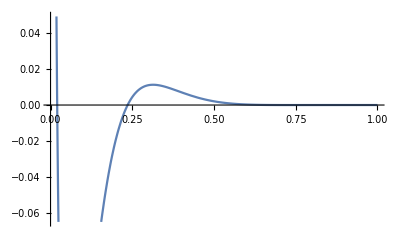

```mathematica
Plot[Hkr[x,0],{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

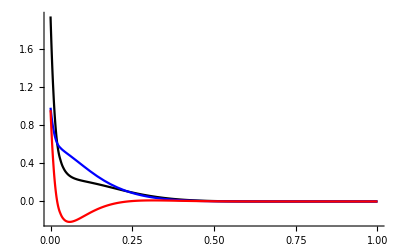

```mathematica
Show[Plot[Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,-0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

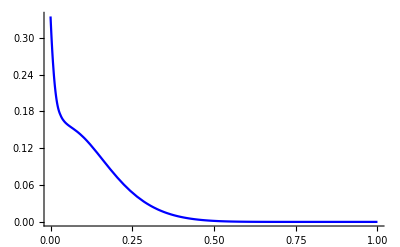

```mathematica
Plot[Hmeson[x,-0.25],{x,0,1},PlotStyle->Blue,PlotRange->All]
```

```mathematica
Hmeson[0.2,-0.25]
```

0.0748592+0. ⅈ

```mathematica
Hmeson[0.16,-0.25]
```

0.100852+0. ⅈ

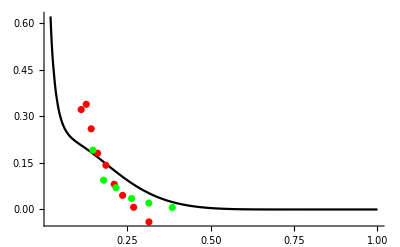

```mathematica
Show[Plot[Hdubar[x,0],{x,0.02,1},PlotStyle->Black,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

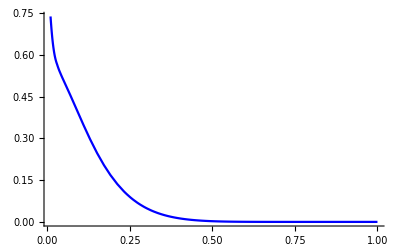

```mathematica
Plot[Hmeson[x,0],{x,0.01,1},PlotStyle->Blue,PlotRange->All]
```

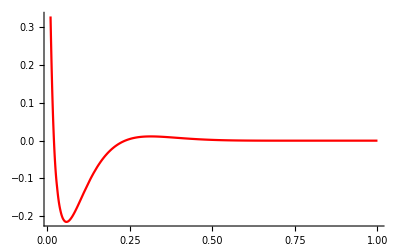

```mathematica
Plot[Hkr[x,0],{x,0.01,1},PlotStyle->Red,PlotRange->All]
```

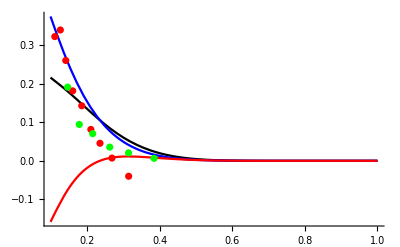

```mathematica
Show[Plot[Hdubar[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

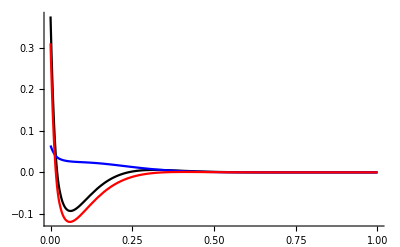

```mathematica
Show[Plot[Hdubar[x,-1],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,-1],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,-1],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

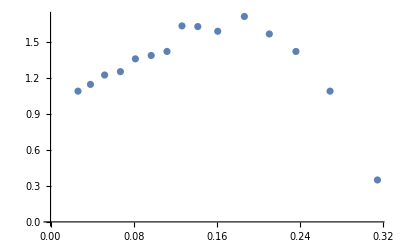

```mathematica
ListPlot[dcuE866data]
```

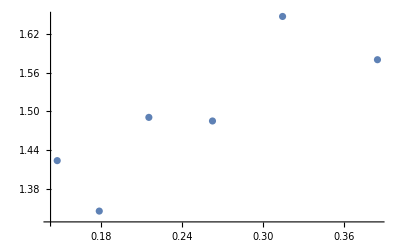

```mathematica
ListPlot[dcuE906data]
```

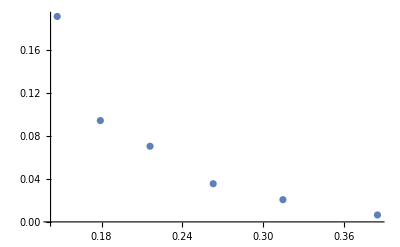

```mathematica
ListPlot[dmuE906]
```

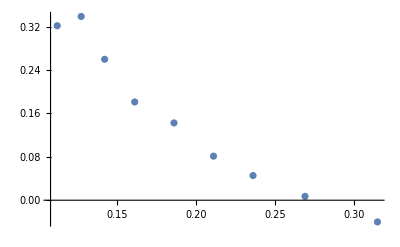

```mathematica
ListPlot[dmuE866]
```

```mathematica
(*好像把纵坐标取大了10倍*)
```

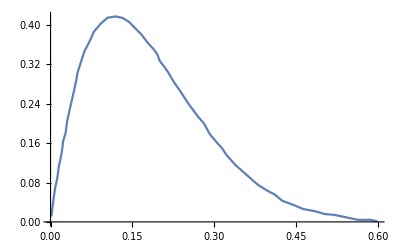

InterpolatingFunction::dmval: Input value {0.0000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListLinePlot[Hexdubardata]
```

```mathematica
GlobalDataxduf1[x_]=Fit[GlobalDataxdu1, {1,x,x^2,x^3,x^4,x^5}, x]
```

28.3159 x^5-41.4659 x^4+23.6004 x^3-6.10382 x^2+0.526924 x+0.0287295

```mathematica
GlobalDataxduf2[x_]=Fit[GlobalDataxdu2, {1,x,x^2,x^3,x^4,x^5}, x]
```

54.0041 x^5-73.5437 x^4+38.4571 x^3-9.20715 x^2+0.824818 x+0.0116936

```mathematica
Hexdubar[x_]=-0.008609374368660145+8.849341692528956 x-61.20048373887701 x^2+163.17446188487307 x^3-197.35237919589093 x^4+90.84866778717655 x^5;
```

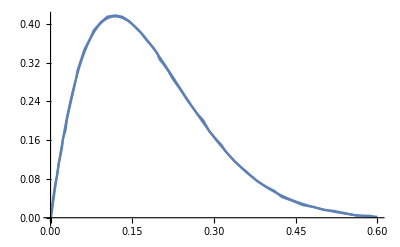

```mathematica
Show[Plot[Hexdubar[x],{x,0,0.6}],ListLinePlot[Hexdubardata]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

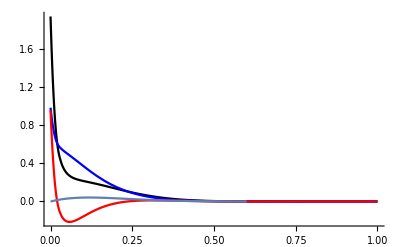

```mathematica
Show[Plot[Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All],Plot[(1/10)*Hexdubar[x],{x,0,0.6}]]
```

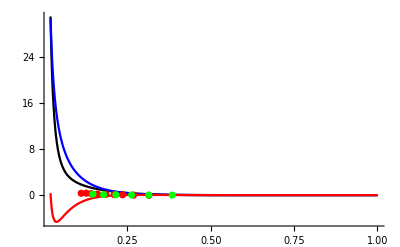

```mathematica
picdubar=Show[Plot[(1/x)*Hdubar[x,0],{x,0.02,1},PlotStyle->Black,PlotRange->All],Plot[(1/x)*Hmeson[x,0],{x,0.02,1},PlotStyle->Blue,PlotRange->All],Plot[(1/x)*Hkr[x,0],{x,0.02,1},PlotStyle->Red,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

```mathematica
pathdubar=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"dubar.pdf"}];
(*Export[pathdubar,picdubar]
```

```mathematica
picxdubar=Show[Plot[Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
pathxdubar=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"xdubar.pdf"}];
(*Export[pathxdubar,picxdubar]
```

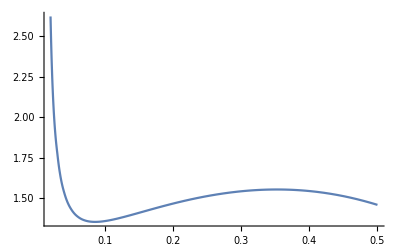

```mathematica
Plot[Hdude[x,0],{x,0.02,0.5},PlotRange->All]
```

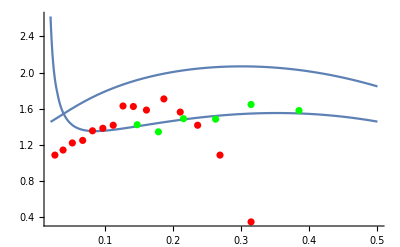

```mathematica
picdcu=Show[Plot[Hdude[x,0],{x,0.02,0.5},PlotRange->All],Plot[Hmede[x,0],{x,0.02,0.5},PlotRange->All],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```

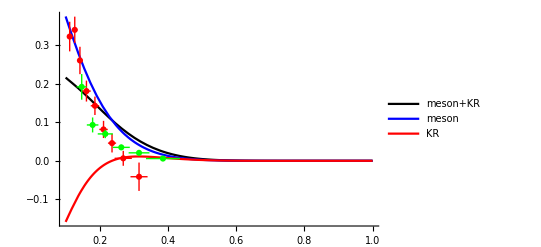
-Graphics-Λ=1

```mathematica
L1=Labeled[Show[Plot[Hdubar[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[Hmeson[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[Hkr[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]],"Λ=1",Top]
```

```mathematica
pathdubarL1=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubarL1.pdf"}];
Export[pathdubarL1,L1]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubarL1.pdf

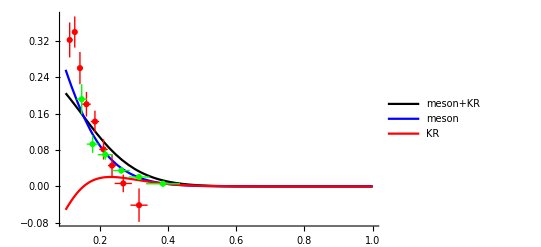
-Graphics-Λ=0.8

```mathematica
L08=Labeled[Show[Plot[HdubarL08[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[HmesonL08[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[HkrL08[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]],"Λ=0.8",Top]
```

```mathematica
pathdubarL08=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubarL08.pdf"}];
Export[pathdubarL08,L08]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubarL08.pdf

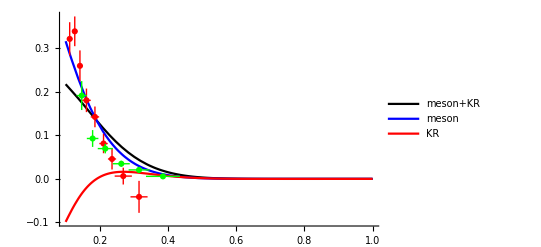
-Graphics-Λ=0.9

```mathematica
L09=Labeled[Show[Plot[HdubarL09[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[HmesonL09[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[HkrL09[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]],"Λ=0.9",Top]
```

```mathematica
pathdubarL09=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubarL09.pdf"}];
Export[pathdubarL09,L09]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubarL09.pdf

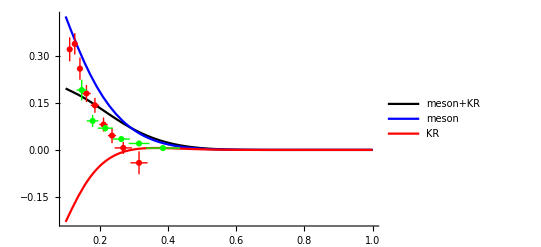
-Graphics-Λ=1.1

```mathematica
L11=Labeled[Show[Plot[HdubarL11[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[HmesonL11[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[HkrL11[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]],"Λ=1.1",Top]
```

```mathematica
pathdubarL11=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubarL11.pdf"}];
Export[pathdubarL11,L11]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubarL11.pdf

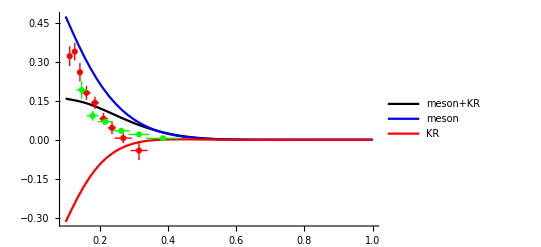
-Graphics-Λ=1.2

```mathematica
L12=Labeled[Show[Plot[HdubarL12[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[HmesonL12[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[HkrL12[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]],"Λ=1.2",Top]
```

```mathematica
pathdubarL12=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubarL12.pdf"}];
Export[pathdubarL12,L12]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubarL12.pdf

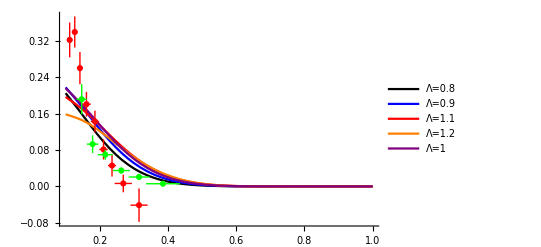

```mathematica
L5=Show[Plot[HdubarL08[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"Λ=0.8"},Above]],Plot[HdubarL09[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"Λ=0.9"},Above]],Plot[HdubarL11[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"Λ=1.1"},Above]],Plot[HdubarL12[x,0],{x,0.1,1},PlotStyle->Orange,PlotRange->All,PlotLegends->Placed[{"Λ=1.2"},Above]],Plot[Hdubar[x,0],{x,0.1,1},PlotStyle->Purple,PlotRange->All,PlotLegends->Placed[{"Λ=1"},Above]],ListPlot[E866dmudatawithbar,PlotStyle->Red],ListPlot[Seaquestdmudatawithbar,PlotStyle->Green]]
```

```mathematica
pathdubarl5=FileNameJoin[{"G:\\calc-online\\gpd\\wangyaoqiu\\pic",
"dubar5L.pdf"}];
Export[pathdubarl5,L5]
```

G:\calc-online\gpd\wangyaoqiu\pic\dubar5L.pdf

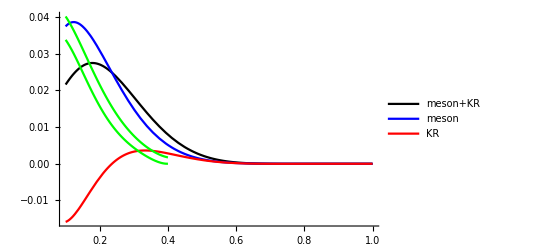
-Graphics-Λ=1

```mathematica
xL1=Labeled[Show[Plot[x*Hdubar[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[x*Hmeson[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[x*Hkr[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]],"Λ=1",Top]
```

```mathematica
pathxdubarl1=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL1.pdf"}];
Export[pathxdubarl1,xL1]
```

G:\output\summary\gpd\zero\1023\xdubarL1.pdf

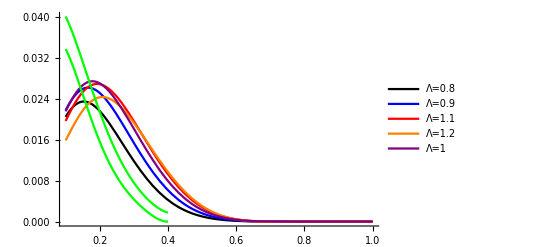

```mathematica
xL5=Show[Plot[x*HdubarL08[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"Λ=0.8"},Above]],Plot[x*HdubarL09[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"Λ=0.9"},Above]],Plot[x*HdubarL11[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"Λ=1.1"},Above]],Plot[x*HdubarL12[x,0],{x,0.1,1},PlotStyle->Orange,PlotRange->All,PlotLegends->Placed[{"Λ=1.2"},Above]],Plot[x*Hdubar[x,0],{x,0.1,1},PlotStyle->Purple,PlotRange->All,PlotLegends->Placed[{"Λ=1"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]]
```

```mathematica
pathxdubarl5=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL5.pdf"}];
Export[pathxdubarl5,xL5]
```

G:\output\summary\gpd\zero\1023\xdubarL5.pdf

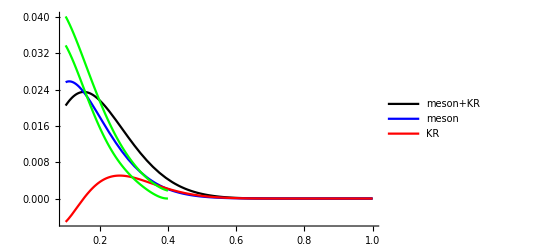
-Graphics-Λ=0.8

G:\output\summary\gpd\zero\1023\xdubarL08.pdf

```mathematica
xL08=Labeled[Show[Plot[x*HdubarL08[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[x*HmesonL08[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[x*HkrL08[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]],"Λ=0.8",Top]
pathxdubarl08=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL08.pdf"}];
Export[pathxdubarl08,xL08]
```

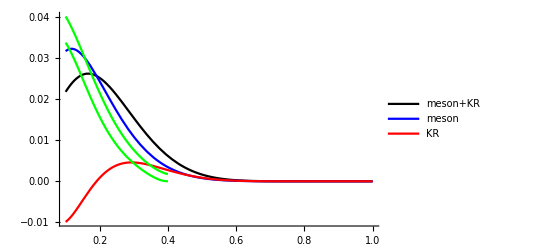
-Graphics-Λ=0.9

G:\output\summary\gpd\zero\1023\xdubarL09.pdf

```mathematica
xL09=Labeled[Show[Plot[x*HdubarL09[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[x*HmesonL09[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[x*HkrL09[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]],"Λ=0.9",Top]
pathxdubarl09=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL09.pdf"}];
Export[pathxdubarl09,xL09]
```

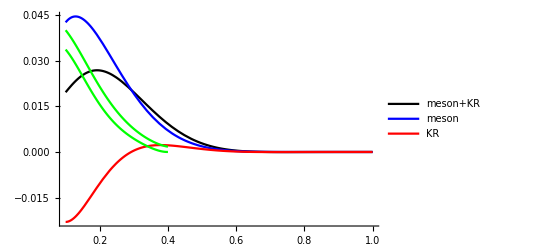
-Graphics-Λ=1.1

G:\output\summary\gpd\zero\1023\xdubarL11.pdf

```mathematica
xL11=Labeled[Show[Plot[x*HdubarL11[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[x*HmesonL11[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[x*HkrL11[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]],"Λ=1.1",Top]
pathxdubarl11=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL11.pdf"}];
Export[pathxdubarl11,xL11]
```

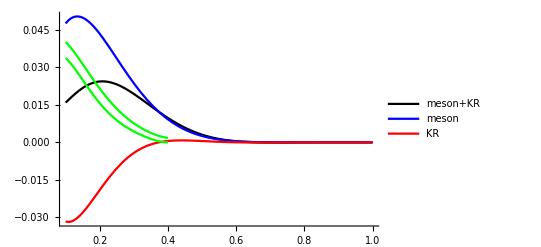
-Graphics-Λ=1.2

G:\output\summary\gpd\zero\1023\xdubarL12.pdf

```mathematica
xL12=Labeled[Show[Plot[x*HdubarL12[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"meson+KR"},Above]],Plot[x*HmesonL12[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All,PlotLegends->Placed[{"meson"},Above]],Plot[x*HkrL12[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All,PlotLegends->Placed[{"KR"},Above]],Plot[GlobalDataxduf1[x],{x,0.1,0.4},PlotStyle->Green],Plot[GlobalDataxduf2[x],{x,0.1,0.4},PlotStyle->Green]],"Λ=1.2",Top]
pathxdubarl12=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\1023",
"xdubarL12.pdf"}];
Export[pathxdubarl12,xL12]
```